```mathematica
Lecture 7:Graphics
```

## Plotting lists and matrices

```mathematica
ListPlot, ArrayPlot,
```

### Exercise Subsection

The Conway recursive sequence is defined by the following cell:

```mathematica
Clear[a]
a[n_]:=a[n]=If[n<=2,1,a[a[n-1]]+a[n-a[n-1]]]
```

Use ListPlot to plot the list of terms of the form a[n]/n where n ranges from 1 to 10000.

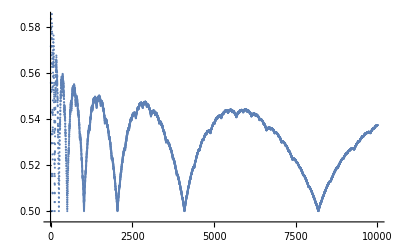

```mathematica
ListPlot[a[#]/#&/@Range@10000]
```

### Exercise Subsection

Illustrate that the number of primes numbers <= n grows approximately at the same rate as the function n/Log[n] by plotting the list of terms of the form PrimePi[n]/(n/Log[n]) for n = 2,...,10^5 and observing that the terms approach a limiting value.

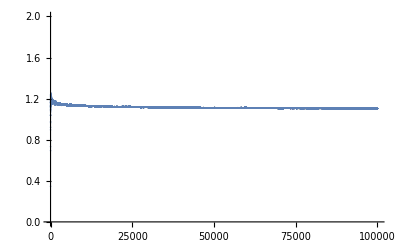

```mathematica
ListPlot[Table[PrimePi[n]/(n/Log[n])//N,{n,2,100000}],PlotRange->{0,2}]
```

### Exercise Subsection

Define the Mobius function mu on the integers such that mu[n] is equal to +1 if n is square free (meaning no square number divides n, see SquareFreeQ) and has an even number of prime factors, -1 if n is squarefree with an odd number of prime factors, and 0 otherwise.  

The Mertens function is defined to send the integer n>=2 to mu[2] + ... + mu[n].  Use ListPlot to plot the first 5000 values of the Mertens function.

```mathematica
mu[n_]:=mu[n]=If[SquareFreeQ@n,(-1)^Length@FactorInteger@n,0]
```

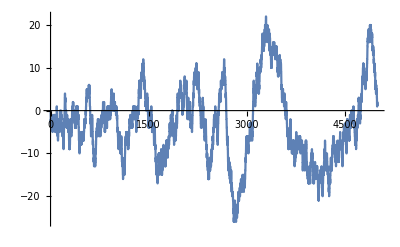

```mathematica
ListPlot[Plus@@(mu/@Range[2,#])&/@Range@5000,Joined->True]
```

### Exercise Subsection

What does the following cell do when evaluated?

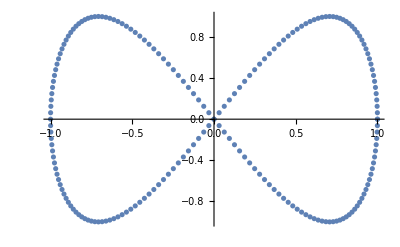

```mathematica
ListPlot[{Cos[#], Sin[2 #]}&/@Range[0,2 Pi,Pi/100]]
```

```mathematica
?RegularExpression
```

## Plotting functions in 2D

```mathematica
Plot,ContourPlot,ParametricPlot,Show, Options,RegionPlot
```

### Exercise Subsection

Use Plot to generate the graphs of Sin[n x]/x on the interval from -Pi to Pi for values of n=1,2,...,5.

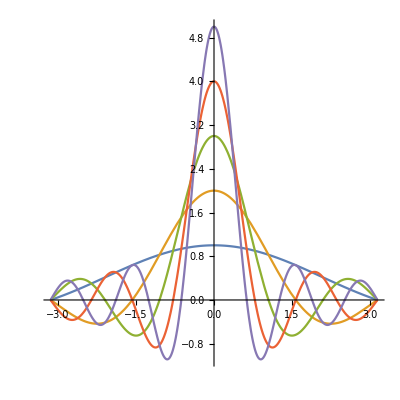

```mathematica
L=Sin[# x]/x&/@Range@5;
Plot[L,{x,-Pi,Pi},PlotRange->All,AspectRatio->1]
```

### Exercise Subsection

```mathematica
Table[RegionPlot[x^3-y^2==k,{x,-5,5},{y,-5,5}],{k,0,2,1/10}]
```

### Exercise Subsection

```mathematica
ContourPlot[Sin[x^2 + y],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics-

### Exercise Subsection

```mathematica
ParametricPlot3D[{Cos[t]Sin[t],Cos[2 t],Sin[3t]},{t,0,3Pi}]
```

-Graphics3D-

## Plotting functions in 3D

```mathematica
Plot3D,ContourPlot3D,ParametricPlot3D
```

## Graphics objects

### Exercise Subsection

```mathematica
?Graphics
```

### Exercise Subsection

Recall from Exercise Set 5 that Thue-Morse sequence is a sequence of lists that begins with the list {0} and then subsequent terms in the sequence are found by replacing each 0 in the previous list with 0, 1 and each 1 with 1, 0.  It can be defined using the function in the next cell:

```mathematica
tm[n_]:=Nest[Flatten[#/.{0->{0,1},1->{1,0}}]&,{0},n]
```

Turn tm[n] into a graphic in the plane using AnglePath together with Line and Graphics (see the documentation for AnglePath for an example).  Beginning at the {0,0}, turn right (using angle -Pi/3) and travel one step forward for each 1 in tm[n] and go straight (using angle 0) and travel one step forward for each 0 in tm[n].  Show the graphic created in this way when n=15.

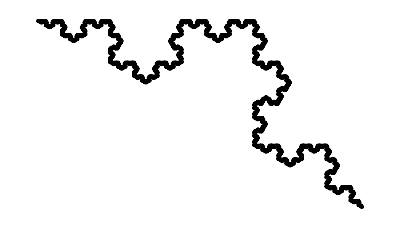

```mathematica
Graphics@Line@AnglePath[tm[15]/.{1->-Pi/3}]
```

### Exercise Subsection

The regular paperfolding sequence (see https://en.wikipedia.org/wiki/Regular_paperfolding_sequence or https://en.wikipedia.org/wiki/Dragon_curve ) is a sequence of bit strings.  The paperfolding sequence can be defined recursively with Paper[0] = {1} and then taking Paper[n] to be the list created by Join-ing the list Paper[n-1], the list {1}, and the list Paper[n-1] in reverse order with each 1 replaced with a 0 and each 0 replaced with a 1.

a. Define the function Paper[n]

b. Turn Paper[n] into a graphic in the plane using AnglePath in together with Line and Graphics (see the documentation for AnglePath for an example).  Beginning at the {0,0}, turn right (using angle -Pi/2) and travel one step forward for each 1 in Paper[n] and turn left (using angle Pi/2) and travel one step forward for each 0 in Paper[n].  Show the graphic created in this way when n=12.

```mathematica
Paper[n_]:=If[n==0,{1},Join[Paper[n-1],{1},Reverse@Paper[n-1]/.{1->0,0->1}]]
```

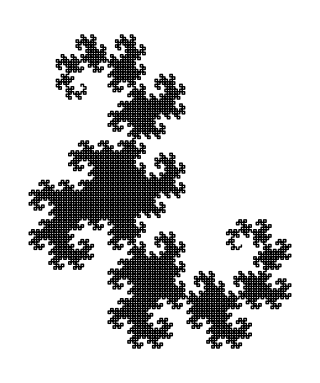

```mathematica
Graphics@Line@AnglePath[Paper[12]/.{1->-Pi/2,0->Pi/2}]
```

## Animations

```mathematica
Animate, ListAnimate, Manipulate
```

### Exercise Subsection

The fundamental theorem of algebra says that every nonconstant polynomial f[x] has a complex root; meaning that there is a complex c such that f[c]=0.  Every complex number c can be expressed in polar form as c = r E^(i t) where r is a positive number and t is an angle between 0 and 2 Pi.  Therefore the fundamental theorem of algebra says there is a positive r and a t between 0 and 2 Pi for which both the real and imaginary parts of f[r E^(i t)] is equal to 0. 

Explain how the below cell can be used to illustrate the validity of the fundamental theorem of algebra for the given polynomial f[x].

```mathematica
f[x_]:=x^3+x^2-x+1;
Manipulate[ParametricPlot[{Re[f[r E^(I t)]],Im[f[r E^(I t)]]},{t,0,2Pi},PlotRange->{-5,5},AspectRatio->1],{r,0,3}]
```

### Exercise Subsection

Let M be a 20x20 matrix (a list of 20 lists, each of length 20) with entries either 0 or 1.

The neighbors of an i,j entry in M are the entries in M that are horizontally, vertically, or diagonally adjacent to the i,j entry.  An entry usually has 8 neighbors unless the entry is in a row or column on the border of M, in which case there can be fewer neighbors. 

a. Define a function Neighbors[M_,{i_,j_}] that inputs a 20x20 matrix M, a row i, and a column j, and outputs the number of neighbors of the i,j entry in M that are equal to 1.

Conway’s game of life is a function that changes M according to the following rules:
1. If an entry in M is 1 and has fewer than two neighbors equal to 1, then the entry changes to 0.
2. If an entry in M is 1 and has more than three neighbors equal to 1, then the entry changes to 0.
3. If an entry is 0 and has exactly three neighbors equal to 1, then the entry changes to 1. 
4. All other entries are unchanged.

b. Define a function Conway[M_] that transforms M using the above rules.

c. Try the command ListAnimate[ArrayPlot/@NestList[Conway,M,100]] where M is the matrix in the next cell.  Then change M to another matrix of your invention to produce another cool looking “movie”.

```mathematica
M={{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0}};
```

```mathematica
Neighbors[M_,{i_,j_}]:=Count[M[[First@#,Last@#]]&/@DeleteCases[{i,j}+#&/@DeleteCases[Tuples[{-1,0,1},2],{0,0}],{a_,b_}/;Or[a==0,b==0,a==21,b==21]],1]
```

```mathematica
Conway[M_]:=Table[
Which[And[M[[i,j]]==1,Neighbors[M,{i,j}]<2],0,
And[M[[i,j]]==1,Neighbors[M,{i,j}]>3],0,
And[M[[i,j]]==0,Neighbors[M,{i,j}]==3],1,
True,M[[i,j]]],{i,20},{j,20}]
```

```mathematica
ListAnimate[ArrayPlot/@NestList[Conway,M,100]]
```